## Lucrare de laborator nr. 2

### Țurcanu Cristian, grupa MIA2201

Ca și temă pentru laboratorul dat am ales statistica terenului folosit pentru agricultură în fiecare țară.

```mathematica
countryList = {Entity["Country","UnitedStates"], Entity["Country","Moldova"], Entity["Country","Brazil"], Entity["Country","China"], Entity["Country","Russia"], Entity["Country","Sweden"], Entity["Country","France"], Entity["Country","Japan"]};
propertyList = {"LandArea","ArableLandArea","CropsLandArea","ArableLandFraction","CropsLandFraction"};
dataOnly=Outer[#1[#2]&, countryList,propertyList];
For[i=1,i<=Length[countryList],i++,PrependTo[dataOnly⟦i⟧,countryList⟦i⟧]];
PrependTo[propertyList, ""];
PrependTo[dataOnly, propertyList];
TableForm[dataOnly]
```

| LandArea | ArableLandArea | CropsLandArea | ArableLandFraction | CropsLandFraction
United States | 9.16192×10^6 km^2 | 1.57737×10^6 km^2 | 19240. km^2 | 17.2439 % | 0.21 %
Moldova | 32891. km^2 | 16817. km^2 | 2897.7 km^2 | 51.1384 % | 8.81 %
Brazil | 8.45942×10^6 km^2 | 557620. km^2 | 75288.8 km^2 | 6.67158 % | 0.89 %
China | 9.32641×10^6 km^2 | 1.19489×10^6 km^2 | 118445. km^2 | 12.6782 % | 1.27 %
Russia | 16377742 km^2 | 1.21649×10^6 km^2 | 18695.4 km^2 | 7.4281 % | 0.11 %
Sweden | 410335. km^2 | 25500. km^2 | 41. km^2 | 6.26059 % | 0.01 %
France | 549970. km^2 | 181264. km^2 | 11076.3 km^2 | 33.1041 % | 2.03 %
Japan | 374744. km^2 | 41420. km^2 | 3372.7 km^2 | 11.3635 % | 0.9 %

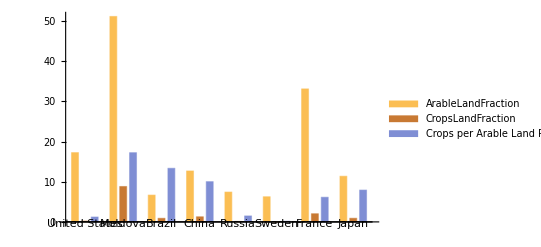

```mathematica
percentageProperties = {"ArableLandFraction","CropsLandFraction"};
percentageData=Outer[#1[#2]&, countryList,percentageProperties];
For[i=1,i<=Length[percentageData],i++,AppendTo[percentageData⟦i⟧,100*percentageData⟦i⟧⟦2⟧/percentageData⟦i⟧⟦1⟧]];
BarChart[percentageData, ChartLabels->{countryList, None}, ChartLegends->Append[percentageProperties,"Crops per Arable Land Ratio"]]
```

În graficul dat comparăm fracția de teren arabil la teritoriul țării, fracția de teren de facto folosit pentru agricultură la teritoriul țării și raportul de teren folosit în agricultură la teren potențial arabil. Observăm că Moldova ocupă locul întâi dintre țările alese la toate categoriile, însă aceste rezultate nu înseamnă mult pur și simplu din cauza diferenței de mărime a teritoriului țărilor, pe care o vom compara în următorul grafic:

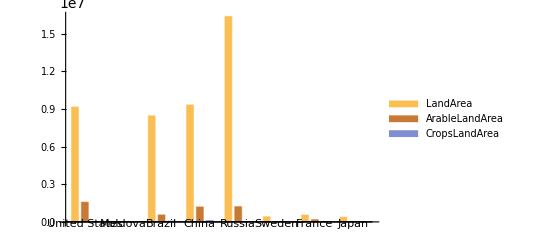

```mathematica
percentageProperties2 = {"LandArea","ArableLandArea","CropsLandArea"};
percentageData2=Outer[#1[#2]&, countryList,percentageProperties2];
BarChart[percentageData2, ChartLabels->{countryList, None}, ChartLegends->percentageProperties2]
```

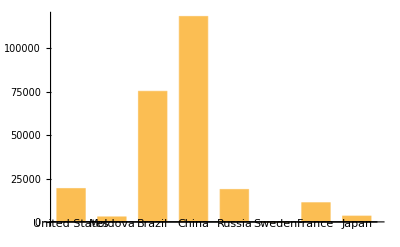

```mathematica
actualProperties = {"CropsLandArea"};
actualData=Outer[#1[#2]&, countryList,actualProperties];
BarChart[actualData, ChartLabels->{countryList, None}]
```

În graficul dat observăm că dintre țările alese China ocupă primul loc după teren folosit în agricultură, ceea ce ne demonstrează folosirea tacticii de agricultură extensivă pentru a obține multă roadă.

```mathematica
data =Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i, CountryData[All]}];
```

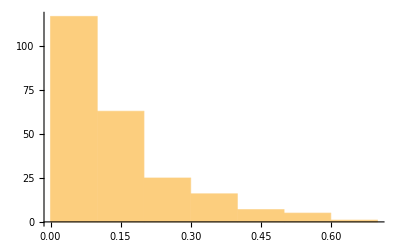

```mathematica
Histogram[data⟦All,5⟧]
```

Graficul dat ne demonstrează faptul că majoritatea țărilor folosesc doar o parte extrem de mică a terenului pentru agricultură.

```mathematica
removeMissing[l_List]:=DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[l,{_,_,_,_,_,_Missing}],{_,_,_,_,_Missing,_}],{_,_,_,_Missing,_,_}],{_,_,_Missing,_,_,_}],{_,_Missing,_,_,_,_}],{_Missing,_,_,_,_,_}]
```

```mathematica
dataNorthAmerica=Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["NorthAmerica"]}]//removeMissing;
dataAsia=Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Asia"]}]//removeMissing;
dataEurope=Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Europe"]}]//removeMissing;
dataAfrica=Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Africa"]}]//removeMissing;
dataSouthAmerica=Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["SouthAmerica"]}]//removeMissing;
```

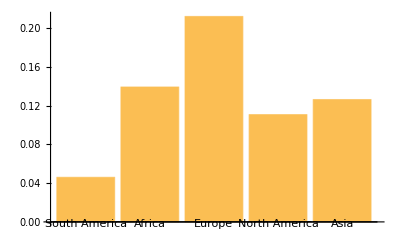

```mathematica
BarChart[{Mean[dataSouthAmerica⟦All,5⟧],Mean[dataAfrica⟦All,5⟧],Mean[dataEurope⟦All,5⟧],Mean[dataNorthAmerica⟦All,5⟧],Mean[dataAsia⟦All,5⟧]}, ChartLabels->{"South America","Africa","Europe","North America","Asia"}]
```

Observăm că după fracția de teren folosit în agricultură Europa ocupă locul întâi

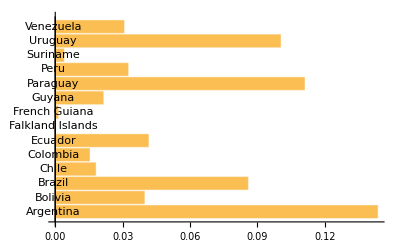

```mathematica
BarChart[dataSouthAmerica⟦All,5⟧,ChartLabels->dataSouthAmerica⟦All,1⟧,BarOrigin->Left]
```

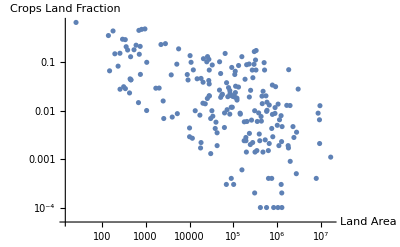

```mathematica
removeMissing2[l_List]:=DeleteCases[DeleteCases[l,{_,_Missing}],{_Missing,_}];
dataArea=Table[{CountryData[i,"LandArea"],CountryData[i,"CropsLandFraction"]},{i,CountryData[]}]//removeMissing2;
ListLogLogPlot[dataArea,{AxesLabel->{"Land Area", "Crops Land Fraction"}}]
```